```mathematica
data = Import["/Users/bbn/Desktop/PhyExp/Exp8.xlsx"]
```

{{{S(cm),DeltaT(ms),,,v/(m/s),v^2,2s},{20.,37.17,37.67,37.26,0.253524,0.0642742,0.4},{30.,31.38,30.82,31.34,0.303827,0.092311,0.6},{40.,26.17,26.85,26.87,0.355739,0.12655,0.8},{50.,24.02,24.05,23.88,0.394997,0.156022,1.},{60.,21.82,21.97,22.05,0.431652,0.186324,1.2},{DeltaS,0.94,0.952,0.95,0.947333,,},{h,15.,15.08,15.,,,},{L,86.29,87.5,87.49,,,}}}

```mathematica
fitData = data[[1]][[2;;6,{-1,-2}]]
deltaS = data[[1]][[7,-3]]
h = data[[1]][[8,2;;4]]*10^-2
l = data[[1]][[9,2;;4]]*10^-2
ft = LinearModelFit[fitData,{x},{x}]
```

{{0.4,0.0642742},{0.6,0.092311},{0.8,0.12655},{1.,0.156022},{1.2,0.186324}}

0.947333

{0.15,0.1508,0.15}

{0.8629,0.875,0.8749}

FittedModel[0.00197212+0.153905 x]

```mathematica
%["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00197212 | 0.00202166 | 0.975498 | 0.401258
x | 0.153905 | 0.00238255 | 64.597 | 8.17448×10^-6

```mathematica
line = Fit[fitData,{1,x},x]
```

0.00197212+0.153905 x

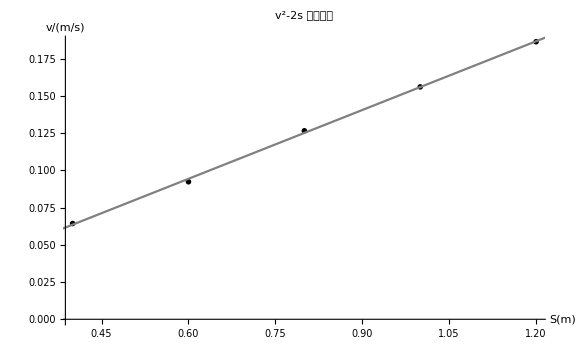

```mathematica
Show[ListPlot[fitData, PlotStyle->Black,PlotMarkers->{Style["X",10]}],Plot[line, {x,0, 1.5},PlotStyle->Gray],AxesLabel->{Style["S(m)",15,Bold],Style["v/(m/s)",15,Bold]},
PlotLabel->Style["v^2-2s  拟合曲线",18,FontFamily->"Adobe Fan Heiti Std", Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]
```

```mathematica
sintheta = Mean[h]*0.1/Mean[l]
```

0.0172535

```mathematica
g = ft["BestFitParameters"][[2]]/sintheta
```

8.92022